# Importance of variables investigation

## Introduction

This blog post demonstrates a procedure for variable importance investigation of mixed categorical and numerical data.

The procedure was used in a previous blog “Classification and association rules for census income data”, [1]. It is implemented in the package VariableImportanceByClassifiers.m, [2]. I took it from [5] (described also below).

The document “Importance of variables investigation guide”, [3], has much more extensive descriptions, explanations, and code for importance of variables investigation using classifiers, Mosaic plots, Decision trees, Association rules, and Dimension reduction.

## Procedure outline

Here we describe the procedure used (that is also done in [3]).

Split the data into training and testing datasets.

Build a classifier with the training set.

Verify using the test set that good classification results are obtained. Find the baseline accuracy.

If the number of variables (attributes) is k for each i, 1≤i≤k:

Shuffle the values of the i-th column of the test data and find the classification success rates.

Compare the obtained k classification success rates between each other and with the success rates obtained by the un-shuffled test data.

The variables for which the classification success rates are the worst are the most decisive.

Note that instead of using the overall baseline accuracy we can make the comparison over the accuracies for selected, more important class labels. (See the examples below.)

The procedure is classifier agnostic. With certain classifiers, Naive Bayesian classifiers and Decision trees, the importance of variables can be directly concluded from their structure obtained after training.

The procedure can be enhanced by using dimension reduction before building the classifiers. (See [3] for an outline.)

## Implementation description

The implementation of the procedure is straightforward in Mathematica -- see the package VariableImportanceByClassifiers.m, [2].

The paclet can be installed and loaded with the commands:

```mathematica
(*PacletInstall["AntonAntonov/VariableImporantanceByClassifiers"];*)Needs["AntonAntonov`VariableImportanceByClassifiers`"];
```

At this point the package has only one function, AccuracyByVariableShuffling, that takes as arguments a ClassifierFunction object, a dataset, optional variable names, and the option “FScoreLabels” that allows the use of accuracies over a custom list of class labels instead of overall baseline accuracy.

Here is the function signature:

AccuracyByVariableShuffling[clFunc_ClassifierFunction, testData_, variableNames_:Automatic, opts:OptionsPattern[] ]

The returned result is an Association structure that contains the baseline accuracy and the accuracies corresponding to the shuffled versions of the dataset. I.e. steps 3 and 4 of the procedure are performed by AccuracyByVariableShuffling. Returning the result in the form Association[___] means we can treat the result as a list with named elements. (Similar to the list structures in Lua and R.)

For the examples in the next section we also going to use the paclet "MosaicPlot", [4], that can be installed and loaded with the following commands:

```mathematica
PacletInstall["AntonAntonov/MosaicPlot"];
Needs["AntonAntonov`MosaicPlot`"];
```

We also use the paclet "DataReshapers" for data summaries and tabulated displays:

```mathematica
PacletInstall["AntonAntonov/DataReshapers"];
Needs["AntonAntonov`DataReshapers`"];
```

## Concrete application over the “Titanic” dataset

1. Load some data.

```mathematica
testSetName = "Titanic"; (* "Mushroom" "Titanic" *)
 trainingSet = ExampleData[{"MachineLearning", testSetName}, "TrainingData"];
 testSet = ExampleData[{"MachineLearning", testSetName}, "TestData"];
```

2. Variable names and unique class labels.

```mathematica
varNames = Flatten[List @@ ExampleData[{"MachineLearning", testSetName}, "VariableDescriptions"]]
```

{passenger class,passenger age,passenger sex,passenger survival}

```mathematica
classLabels = Union[ExampleData[{"MachineLearning", testSetName}, "Data"][[All, -1]]]
```

{died,survived}

3. Here is a data summary.

```mathematica
Grid[List@RecordsSummary[(Flatten/@(List@@@Join[trainingSet,testSet]))/._Missing->0,varNames],Dividers->All,Alignment->{Left,Top}]
```

1 passenger class
3rd | 709
1st | 323
2nd | 277 | 2 passenger age
Min | 0
1st Qu | 7.
Mean | 23.8775
Median | 24.
3rd Qu | 35.
Max | 80. | 3 passenger sex
male | 843
female | 466 | 4 passenger survival
died | 809
survived | 500

4. Make the classifier.

```mathematica
clFunc = Classify[trainingSet, Method -> "RandomForest"]
```

ClassifierFunction[…]

5. Obtain accuracies after shuffling.

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames]
```

<|None→0.778626,passenger class→0.725191,passenger age→0.768448,passenger sex→0.631043|>

6. Tabulate the results.

```mathematica
Grid[
    Prepend[
      List @@@ Normal[accs/First[accs]],
      Style[#, Bold, Blue, FontFamily -> "Times"] & /@ {"shuffled variable", "accuracy ratio"}],
    Alignment -> Left, Dividers -> All]
```

shuffled variable | accuracy ratio
None | 1.
passenger class | 0.931373
passenger age | 0.986928
passenger sex | 0.810458

7. Further confirmation of the found variable importance can be done using the mosaic plots.
    We can see that female passengers are much more likely to survive and especially female passengers from first and second class.

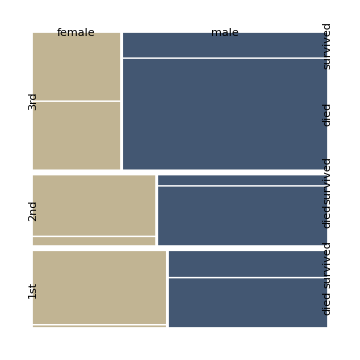

```mathematica
t = DeleteCases[(Flatten /@ (List @@@ trainingSet)),{___,_Missing,___}];
 MosaicPlot[t[[All, {1,3,4}]], ColorRules -> {2-> ColorData[7, "ColorList"]} ,"LabelRotation"->{{1,0.45},{0,1}},ImageSize->Medium]
```

5a. In order to use F-scores instead of overall accuracy the desired class labels are specified with
    the option "ClassLabels".

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames, "ClassLabels" -> classLabels]
```

<|None→{0.753247,0.870588},passenger class→{0.680124,0.661972},passenger age→{0.750799,0.9},passenger sex→{0.66879,0.582278}|>

5b. Here is another example that uses the class label with the smallest F-score.
    (Probably the most important since it is most misclassified).

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames,
                                     "ClassLabels" -> Position[#, Min[#]][[1, 1, 1]] &@
                                                                ClassifierMeasurements[clFunc, testSet, "FScore"]]
```

<|None→{0.870588},passenger class→{0.731343},passenger age→{0.842697},passenger sex→{0.552632}|>

5c. It is good idea to verify that we get the same results using different classifiers. Below is given code that computes the shuffled accuracies and returns the relative damage scores for a set of methods of Classify.

```mathematica
mres=Association@Map[
Function[{clMethod},
cf=Classify[trainingSet,Method->clMethod];
accRes=AccuracyByVariableShuffling[cf,testSet,varNames,"ClassLabels"->"survived"];
clMethod->(accRes[None]-Rest[accRes])/accRes[None]
],{"LogisticRegression","NearestNeighbors","RandomForest","SupportVectorMachine"}] ;
```

```mathematica
Dataset[mres]
```

## Concrete application over the “Mushroom” dataset

1. Load some data.

```mathematica
testSetName = "Mushroom"; 
 trainingSet = ExampleData[{"MachineLearning", testSetName}, "TrainingData"];
 testSet = ExampleData[{"MachineLearning", testSetName}, "TestData"];
```

2. Variable names and unique class labels.

```mathematica
varNames = Flatten[List @@ ExampleData[{"MachineLearning", testSetName}, "VariableDescriptions"]];
varNames[[-1]]="edibility of mushroom";
varNames
```

{cap-shape,cap-surface,cap-color,bruises?,odor,gill-attachment,gill-spacing,gill-size,gill-color,stalk-shape,stalk-root,stalk-surface-above-ring,stalk-surface-below-ring,stalk-color-above-ring,stalk-color-below-ring,veil-type,veil-color,ring-number,ring-type,spore-print-color,population,habitat,edibility of mushroom}

```mathematica
classLabels = Union[ExampleData[{"MachineLearning", testSetName}, "Data"][[All, -1]]]
```

{edible,poisonous}

3. Here is a data summary.

```mathematica
Grid[ArrayReshape[RecordsSummary[(Flatten/@(List@@@Join[trainingSet,testSet]))/._Missing->0,varNames],{6,4},""],Dividers->All,Alignment->{Left,Top}]
```

1 cap-shape
convex | 3656
flat | 3152
knobbed | 828
bell | 452
sunken | 32
conical | 4 | 2 cap-surface
scaly | 3244
smooth | 2556
fibrous | 2320
grooves | 4 | 3 cap-color
brown | 2284
gray | 1840
red | 1500
yellow | 1072
white | 1040
buff | 168
(Other) | 220 | 4 bruises?
False | 4748
True | 3376
5 odor
none | 3528
foul | 2160
fishy | 576
spicy | 576
almond | 400
anise | 400
(Other) | 484 | 6 gill-attachment
free | 7914
attached | 210 | 7 gill-spacing
close | 6812
crowded | 1312 | 8 gill-size
broad | 5612
narrow | 2512
9 gill-color
buff | 1728
pink | 1492
white | 1202
brown | 1048
gray | 752
chocolate | 732
(Other) | 1170 | 10 stalk-shape
tapering | 4608
enlarging | 3516 | 11 stalk-root
bulbous | 3776
0 | 2480
equal | 1120
club | 556
rooted | 192 | 12 stalk-surface-above-ring
smooth | 5176
silky | 2372
fibrous | 552
scaly | 24
13 stalk-surface-below-ring
smooth | 4936
silky | 2304
fibrous | 600
scaly | 284 | 14 stalk-color-above-ring
white | 4464
pink | 1872
gray | 576
brown | 448
buff | 432
orange | 192
(Other) | 140 | 15 stalk-color-below-ring
white | 4384
pink | 1872
gray | 576
brown | 512
buff | 432
orange | 192
(Other) | 156 | 16 veil-type
partial | 8124
17 veil-color
white | 7924
brown | 96
orange | 96
yellow | 8 | 18 ring-number
one | 7488
two | 600
none | 36 | 19 ring-type
pendant | 3968
evanescent | 2776
large | 1296
flaring | 48
none | 36 | 20 spore-print-color
white | 2388
brown | 1968
black | 1872
chocolate | 1632
green | 72
buff | 48
(Other) | 144
21 population
several | 4040
solitary | 1712
scattered | 1248
numerous | 400
abundant | 384
clustered | 340 | 22 habitat
woods | 3148
grasses | 2148
paths | 1144
leaves | 832
urban | 368
meadows | 292
waste | 192 | 23 edibility of mushroom
edible | 4208
poisonous | 3916 |

4. Make the classifier.

```mathematica
clFunc = Classify[trainingSet, Method -> "RandomForest"]
```

ClassifierFunction[…]

5. Obtain accuracies after shuffling.

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames]
```

<|None→1.,cap-shape→1.,cap-surface→1.,cap-color→0.99959,bruises?→0.99918,odor→0.783019,gill-attachment→1.,gill-spacing→0.99959,gill-size→0.997949,gill-color→0.99959,stalk-shape→1.,stalk-root→0.99959,stalk-surface-above-ring→1.,stalk-surface-below-ring→0.99959,stalk-color-above-ring→1.,stalk-color-below-ring→0.99959,veil-type→1.,veil-color→1.,ring-number→1.,ring-type→0.99959,spore-print-color→0.982363,population→0.99918,habitat→1.|>

6. Tabulate the results.

```mathematica
Grid[
    Prepend[
      List @@@ Normal[accs/First[accs]],
      Style[#, Bold, Blue, FontFamily -> "Times"] & /@ {"shuffled variable", "accuracy ratio"}],
    Alignment -> Left, Dividers -> All]
```

shuffled variable | accuracy ratio
None | 1.
cap-shape | 1.
cap-surface | 1.
cap-color | 0.99959
bruises? | 0.99918
odor | 0.783019
gill-attachment | 1.
gill-spacing | 0.99959
gill-size | 0.997949
gill-color | 0.99959
stalk-shape | 1.
stalk-root | 0.99959
stalk-surface-above-ring | 1.
stalk-surface-below-ring | 0.99959
stalk-color-above-ring | 1.
stalk-color-below-ring | 0.99959
veil-type | 1.
veil-color | 1.
ring-number | 1.
ring-type | 0.99959
spore-print-color | 0.982363
population | 0.99918
habitat | 1.

7. Further confirmation of the found variable importance can be done using the mosaic plots.
    Looking at the plot we can see why “odor” is so decisive -- the odor values for “poisonous“ and “edible” intersect very little.

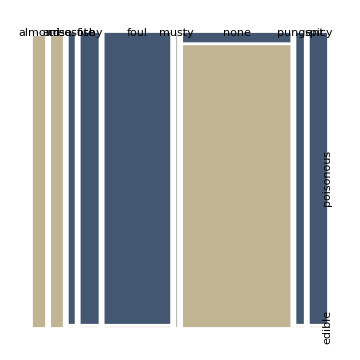

```mathematica
t = (Flatten /@ (List @@@ trainingSet));
 MosaicPlot[t[[All, {5,-1}]],"FirstAxis"->"Top", "LabelRotation"->{{1,0.5},{0,1}},ColorRules -> {2 -> ColorData[7, "ColorList"]},ImageSize->Medium ]
```

Here is a mosaic plot showing the conditional probabilities from a different direction.

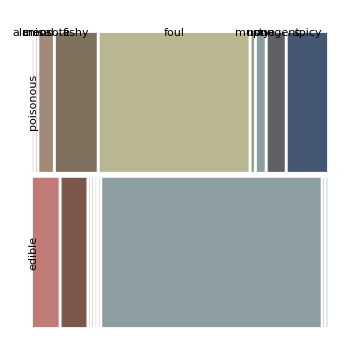

```mathematica
t = (Flatten /@ (List @@@ trainingSet));
 MosaicPlot[t[[All, {-1,5}]],"FirstAxis"->"Left", "LabelRotation"->{{1,0.5},{0,1}},ColorRules -> {2-> ColorData[7, "ColorList"]} ,ImageSize->Medium]
```

5a. In order to use F-scores instead of overall accuracy the desired class labels are specified with
    the option "ClassLabels".

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames, "ClassLabels" -> classLabels]
```

<|None→{1.,1.},cap-shape→{1.,1.},cap-surface→{1.,1.},cap-color→{0.999209,1.},bruises?→{0.999209,1.},odor→{0.816794,0.761716},gill-attachment→{1.,1.},gill-spacing→{0.998419,1.},gill-size→{0.996057,1.},gill-color→{1.,1.},stalk-shape→{1.,1.},stalk-root→{1.,1.},stalk-surface-above-ring→{1.,1.},stalk-surface-below-ring→{1.,1.},stalk-color-above-ring→{1.,1.},stalk-color-below-ring→{0.999209,1.},veil-type→{1.,1.},veil-color→{1.,1.},ring-number→{1.,1.},ring-type→{0.999209,1.},spore-print-color→{0.980937,0.976251},population→{0.998419,1.},habitat→{1.,1.}|>

5b. Here is another example that uses the class label with the smallest F-score.
    (Probably the most important since it is most misclassified).

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames,
                                     "ClassLabels" -> Position[#, Min[#]][[1, 1, 1]] &@
                                                                ClassifierMeasurements[clFunc, testSet, "FScore"]]
```

<|None→{1.},cap-shape→{1.},cap-surface→{1.},cap-color→{1.},bruises?→{0.999209},odor→{0.821117},gill-attachment→{1.},gill-spacing→{0.998419},gill-size→{0.996843},gill-color→{0.999209},stalk-shape→{1.},stalk-root→{0.999209},stalk-surface-above-ring→{1.},stalk-surface-below-ring→{0.999209},stalk-color-above-ring→{1.},stalk-color-below-ring→{1.},veil-type→{1.},veil-color→{1.},ring-number→{1.},ring-type→{0.998419},spore-print-color→{0.980846},population→{0.998419},habitat→{1.}|>

5c. It is good idea to verify that we get the same results using different classifiers. Below is given code that computes the shuffled accuracies and returns the relative damage scores for a set of methods of Classify.

```mathematica
mres=Association@Map[
Function[{clMethod},
cf=Classify[trainingSet,Method->clMethod];
accRes=AccuracyByVariableShuffling[cf,testSet,varNames];
clMethod->(accRes[None]-Rest[accRes])/accRes[None]
],{"LogisticRegression","NearestNeighbors","RandomForest","SupportVectorMachine"}] ;
Dataset[mres]
```

## References

[1] Anton Antonov, “Classification and association rules for census income data”, (2014), MathematicaForPrediction at WordPress.com.

[2] Anton Antonov, Variable importance determination by classifiers implementation in Mathematica, (2015), source code at MathematicaForPrediction at GitHub,  https://github.com/antononcube/MathematicaForPrediction, package VariableImportanceByClassifiers.m.

[3] Anton Antonov, “Importance of variables investigation guide”, (2016),  MathematicaForPrediction at GitHub.

[4] Anton Antonov, MosaicPlot WL paclet, (2023), Wolfram Language Paclet Repository.

[5] Leo Breiman et al., Classification and regression trees, Chapman & Hall, 1984, ISBN-13: 978-0412048418.

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/VariableImportanceByClassifiers

AntonAntonov`VariableImportanceByClassifiers`

AntonAntonov/VariableImportanceByClassifiers/tutorial/Importanceofvariablesinvestigation

### Keywords